## Experiments

```mathematica
getBestNE[nes_]:=Module[{sel,maxVal},


sel=Select[nes,#[[2]]==#[[3]]&];
(*Find the maximum value among the second numbers*)
maxVal=Max[sel[[All,2]]];
(*Select the first element with that maximum value*)
If[sel==={},{},
First[Select[sel,#[[2]]==maxVal&]]
]]

getBestNE[Flatten[ParallelTable[Module[{matA,matB,m,n,neCells,commonOpts,verticalLines,horizontalLines,nashRects,ne,},(*Compute payoff matrices and dimensions*)matA=alicesScores/. {a->A,b->A,γ->Γ};
matB=bobsScores/. {a->A,b->A,γ->Γ};
{m,n}=Dimensions[matA];
(*Find pure Nash equilibria*)
ne =numericNashEquilibria[matA//Chop,matB//Chop]; 
getBestNE[ne]~Join~{A,Γ}
],{A,0.,10.,1/10},{Γ,0,π/2,π/2 1/4}],1]]
```

Part::partw: Part 3 of {0.,π/4} does not exist.

Part::partw: Part 3 of {0.,(3 π)/8} does not exist.

Part::partw: Part 3 of {0.,π/2} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{{2,2},2.25,2.25,1.,π/4}

```mathematica
{{6,6},1.961226184366848,1.961226184366848,9.,(19 π)/80}
```

```mathematica
s1 = 400;
s2 = 400;

MatrixPlot[ParallelTable[Module[{matA,matB,m,n,neCells,commonOpts,verticalLines,horizontalLines,nashRects,ne,bne},(*Compute payoff matrices and dimensions*)matA=alicesScores/. {a->A,b->A,γ->Γ};
matB=bobsScores/. {a->A,b->A,γ->Γ};
{m,n}=Dimensions[matA];
(*Find pure Nash equilibria*)
ne =numericNashEquilibria[matA//Chop,matB//Chop]; 
bne = getBestNE[ne];
If[Length[bne]>=2,
bne[[2]],-1]
],{A,0.,20.,10./s1},{Γ,0,π/2,Pi/2 1/s2}],PlotLegends->Automatic]
```

-Graphics-

```mathematica
s1 = 40;
s2 = 40;

frames = ParallelTable[MatrixPlot[Table[Module[{matA,matB,m,n,neCells,commonOpts,verticalLines,horizontalLines,nashRects,ne,bne},(*Compute payoff matrices and dimensions*)matA=alicesScores/. {a->A,b->B,γ->Γ};
matB=bobsScores/. {a->A,b->B,γ->Γ};
{m,n}=Dimensions[matA];
(*Find pure Nash equilibria*)
ne =numericNashEquilibria[matA//Chop,matB//Chop]; 
bne = getBestNE[ne];
If[Length[bne]>=2,
bne[[2]],-1]
],{A,0.,10.,10./40},{B,0.,10.,10./40}],ColorFunction->colorFunc,ColorFunctionScaling->False,PlotLegends->BarLegend[{colorFunc,{-1,5}}]],{Γ,0,π/5,Pi/2 1/80}];
```

```mathematica
ListAnimate[frames]
```

```mathematica
colorFunc
```

ColorDataFunction[Function[x,ColorData[TemperatureMap][Rescale[x,{-1,3}]]],ColorFunctionScaling→False]

Blend[{{-1,Black},{0,Red},{2,Orange},{3,Yellow},{4,Green},{5,Blue}},#1]&

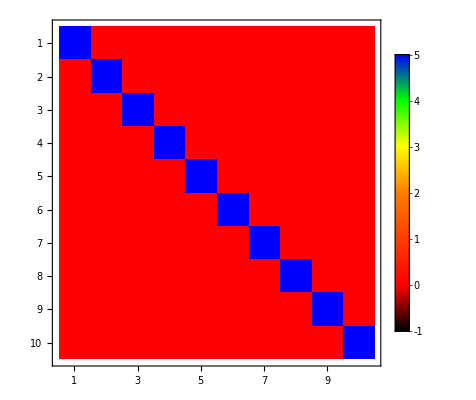

```mathematica
colorFunc=(Blend[{{-1,Black},{0,Red},{2,Orange},{3,Yellow},{4,Green},{5,Blue}},#]&)
min =-1;
max = 2;
MatrixPlot[IdentityMatrix[10]*10,ColorFunction->colorFunc,ColorFunctionScaling->False,PlotLegends->BarLegend[{colorFunc,{-1,5}}]]
```

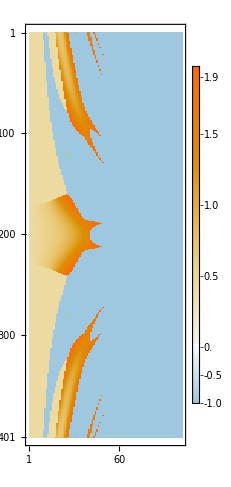

```mathematica
s1 = 200;
s2 = 100;

MatrixPlot[ParallelTable[Module[{matA,matB,m,n,neCells,commonOpts,verticalLines,horizontalLines,nashRects,ne,bne},(*Compute payoff matrices and dimensions*)matA=alicesScores/. {a->A,b->A,γ->Γ};
matB=bobsScores/. {a->A,b->A,γ->Γ};
{m,n}=Dimensions[matA];
(*Find pure Nash equilibria*)
ne =numericNashEquilibria[matA//Chop,matB//Chop]; 
bne = getBestNE[ne];
If[Length[bne]>=2,
bne[[2]],-1]
],{A,-10,10.,10./s1},{Γ,0,π/2,Pi/2 1/s2}],PlotLegends->Automatic]
```

```mathematica
s1 = 200;
s2 = 200;
data = ParallelTable[Module[{matA,matB,m,n,neCells,commonOpts,verticalLines,horizontalLines,nashRects,ne,bne},(*Compute payoff matrices and dimensions*)matA=alicesScores/. {a->A,b->A,γ->Γ};
matB=bobsScores/. {a->A,b->A,γ->Γ};
{m,n}=Dimensions[matA];
(*Find pure Nash equilibria*)
ne =numericNashEquilibria[matA//Chop,matB//Chop]; 
bne = getBestNE[ne]~Join~{A,Γ};
If[Length[bne]>=2,
bne,{{},-1,-1}~Join~{A,Γ}]
],{A,0.,10.,10./s1},{Γ,0,π/2,Pi/2 1/s2}];
```

```mathematica
Select[Flatten[data,1],#[[2]]>1.97&]
```

{{{7,7},1.97299,1.97299,3.6,(6 π)/25},{{6,6},1.97299,1.97299,8.9,(6 π)/25}}

```mathematica
strategySpace[[2]]
```

{{ⅈ,0},{0,-ⅈ}}

```mathematica
strategySpace[[4]]
```

{{0,-ⅈ},{ⅈ,0}}

```mathematica
DensityPlot[Max[numericNashEquilibria[alicesScores/.{a->A,b->B,γ->2 ArcTan[√(5-2 √6)]}//Simplify,bobsScores/.{a->A,b->B,γ->2 ArcTan[√(5-2 √6)]}//Simplify][[;;,2]]],{B,0,3},{A,0,3}]
```

-Graphics-

```mathematica
Max[Table[Max[numericNashEquilibria[alicesScores/.{a->A,b->B,γ->2 ArcTan[√(5-2 √6)]}//Simplify,bobsScores/.{a->A,b->B,γ->2 ArcTan[√(5-2 √6)]}//Simplify][[;;,1]]],{B,1,1.75,.01},{A,1,1.75,.01}]]
```

4

```mathematica
E//N
```

2.71828

```mathematica
d = {{0,-1},{1,0}}
```

{{0,-1},{1,0}}

```mathematica
d.d
```

{{-1,0},{0,-1}}

```mathematica
Manipulate[Module[{matA,matB,m,n,neCells,commonOpts,verticalLines,horizontalLines,nashRects,ne},(*Compute payoff matrices and dimensions*)matA=alicesScores/. {a->A,b->B,γ->Γ};
matB=bobsScores/. {a->A,b->B,γ->Γ};
{m,n}=Dimensions[matA];
(*Find pure Nash equilibria*)
ne =numericNashEquilibria[matA,matB]; 

ne],{A,0.,10.},{B,0.,10.},{{Γ,2 √(5-2 √6)-.01},0,π/2}]
```

Set::shape: Lists {m$4399, n$4399} and {} are not the same shape.

Set::shape: Lists {m$4404, n$4404} and {} are not the same shape.

Set::shape: Lists {Global`m$2862, Global`n$2862} and {}
     are not the same shape.

```mathematica
Manipulate[Module[{matA,matB,m,n,neCells,commonOpts,verticalLines,horizontalLines,nashRects,ne,p},(*Compute payoff matrices and dimensions*)
Plot[
matA=alicesScores/. {a->A,b->B,γ->Γ};
matB=bobsScores/. {a->A,b->B,γ->Γ};
{m,n}=Dimensions[matA];
(*Find pure Nash equilibria*)
ne =numericNashEquilibria[matA,matB]; 

If[Length[ne]==1,

(*if it contains {5,7}*)

p = Position[ne,{{3,4},_,_}];


If[Length[p]==1,ne[[p[[1,1]]]][[2]],0],



0],{Γ,0.,π/2}]]

,{A,0.,10.},{B,0.,100.}]
```

Set::shape: Lists {m$4142, n$4142} and {} are not the same shape.

Set::shape: Lists {m$4148, n$4148} and {} are not the same shape.

Set::shape: Lists {m$4565,n$4565} and {} are not the same shape.

```mathematica
ListAnimate[Table[Module[{matA,matB,m,n,neCells,commonOpts,verticalLines,horizontalLines,nashRects,ne,p},(*Compute payoff matrices and dimensions*)
Show[Table[
matA=alicesScores/. {a->A,b->0,γ->Γ};
matB=bobsScores/. {a->A,b->0,γ->Γ};
{m,n}=Dimensions[matA];
(*Find pure Nash equilibria*)
ne =numericNashEquilibria[matA,matB]; 
ListPlot[ne[[All,{2,3}]],PlotRange->{{0,4},{0,4}},AspectRatio->1],
{Γ,0,π/5,π/100}]]
]

,{A,0.,10.,.1}]]
```